```mathematica
x= {0.074195,0.077316,0.144645,0.18457,0.0155,0.01528,0.016587,0.017259,.040169,0.015218,0.016171,0.017171,0.040309,0.074283,0.07781,0.094418,0.074309,0.094648}
```

{0.074195,0.077316,0.144645,0.18457,0.0155,0.01528,0.016587,0.017259,0.040169,0.015218,0.016171,0.017171,0.040309,0.074283,0.07781,0.094418,0.074309,0.094648}

```mathematica
y= {2.1849,2.1592,1.764,1.5651,2.0918,2.4848,2.4551,2.4401,2.0515,2.5714, 2.56,2.5556,2.288, 1.9297, 1.9028, 1.7547, 2.1009, 1.9461}
```

{2.1849,2.1592,1.764,1.5651,2.0918,2.4848,2.4551,2.4401,2.0515,2.5714,2.56,2.5556,2.288,1.9297,1.9028,1.7547,2.1009,1.9461}

```mathematica
yerror={0.15514490239317819,0.1553162159181749,0.1671170694283444,0.18050930522739414,0.15843789604945796,0.15847302415473757,0.15826673160138308,0.1581629161533197,0.1555579256897927,0.15848295339267096,0.15833176501151094,0.15817642389167758,0.15554768476068512,0.15514925342817068,0.15534653499563753,0.15687047188856273,0.15515054428971956,0.1568983875091363}
```

{0.155145,0.155316,0.167117,0.180509,0.158438,0.158473,0.158267,0.158163,0.155558,0.158483,0.158332,0.158176,0.155548,0.155149,0.155347,0.15687,0.155151,0.156898}

```mathematica
plotyvalues=Table[Around[y[[i]],yerror[[i]]],{i,1,Length[y]}]
```

{2.180.16,2.160.16,1.760.17,1.570.18,2.090.16,2.480.16,2.460.16,2.440.16,2.050.16,2.570.16,2.560.16,2.560.16,2.290.16,1.930.16,1.900.16,1.750.16,2.100.16,1.950.16}

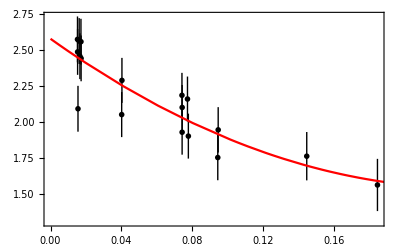

```mathematica
Show[ListPlot[Transpose[{x,plotyvalues}],PlotTheme->"Monochrome"], Plot[2.5754552237209665-8.737856713302271 c+18.500684807545397 c^2,{c,0,1},PlotStyle->{Red}],Frame->True]
```

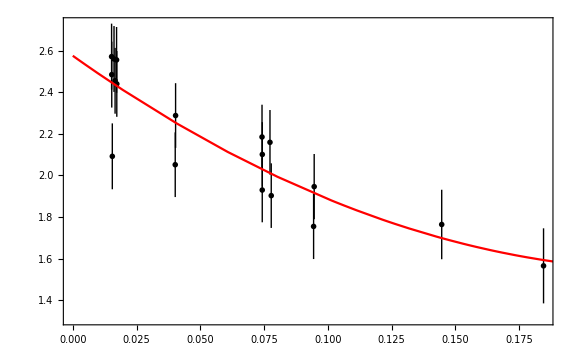

```mathematica
Show[%5,ImageSize->Large]
```

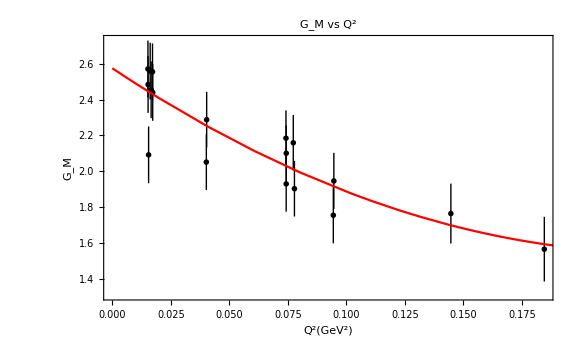

```mathematica
Show[%6,FrameLabel->{{HoldForm[Subscript[G, "M"]],None},{HoldForm[(Q^2)[GeV^2]],None}},PlotLabel->HoldForm[Subscript[G, "M"] vs Q^2],LabelStyle->{14,GrayLevel[0],Bold}]
```

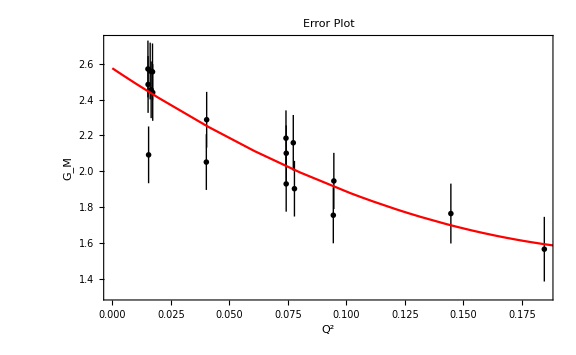

```mathematica
Show[%6,FrameLabel->{{HoldForm[Subscript[G, "M"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Error Plot],LabelStyle->{14,GrayLevel[0],Bold}]
```

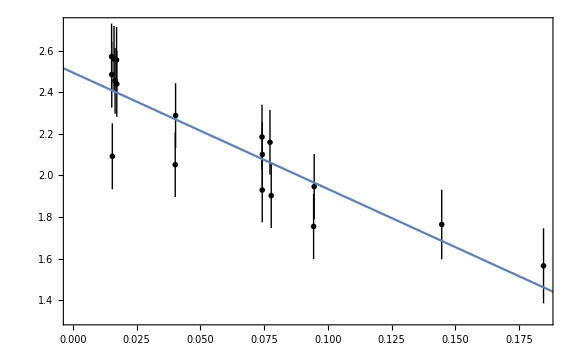

```mathematica
Show[%13,ImageSize->Large]
```

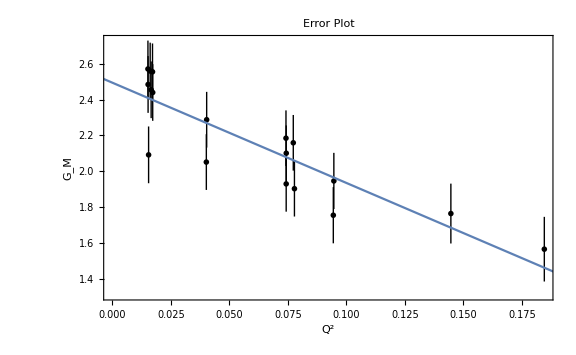

```mathematica
Show[%14,FrameLabel->{{HoldForm[Subscript["G", "M"]],None},{HoldForm[Q^2],None}},PlotLabel->HoldForm[Error Plot],LabelStyle->{12,GrayLevel[0],Bold}]
```

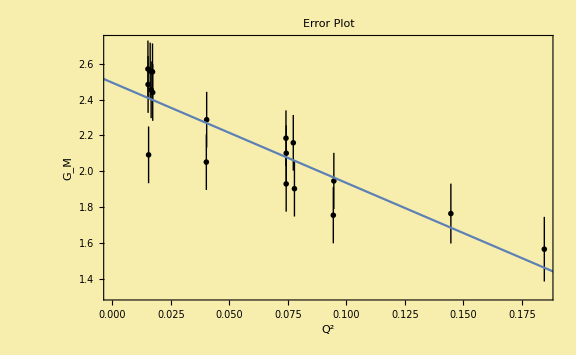

```mathematica
Show[%15,Background->RGBColor[0.97,0.93,0.68]]
```

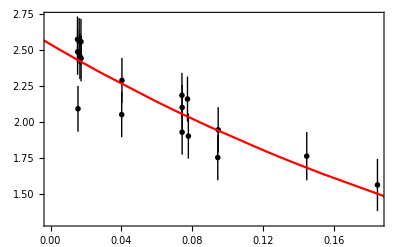

```mathematica
Show[ListPlot[Transpose[{x,plotyvalues}],PlotTheme->"Monochrome"], Plot[2.5369781307297643 ⅇ^(-2.8332539983226597 t),{t,-6.353119067565541,6.353119067565541},PlotStyle->{Red}],Frame->True]
```

```mathematica
Show[%6,FrameLabel->{{HoldForm[Subscript[G, "M"]],None},{HoldForm[(Q^2)[GeV^2]],None}},PlotLabel->HoldForm[Subscript[G, "M"] vs Q^2],LabelStyle->{14,GrayLevel[0],Bold}]
```

-Graphics-